```mathematica
(*
https://arxiv.org/pdf/1707.02792.pdf
*)
```

```mathematica
H[a_,b_,c_,d_,x_]:=If[x≤1,Gamma[a+b]/(Gamma[c-a]*Gamma[a+d])*x^a*Hypergeometric2F1[a+b,1+a-c,a+d,x],Gamma[a+b]/(Gamma[d-b]*Gamma[b+c])*1/x^b * Hypergeometric2F1[a+b,1+b-d,b+c,1/x]];
```

```mathematica
F[q_,E_,L_]:=If[q≠0,3*Gamma[6-q]/(2*(2*Pi)^(5/2)*Gamma[q/2])*E^(7/2-q)*H[0,q/2,9/2-q,1,L^2/(2*E)],3/(7*Pi^3)*(2*E)^(7/2)]
```

```mathematica
NIntegrate[F[-1,e,0.01],{e,0,1}]
```

0.0379153

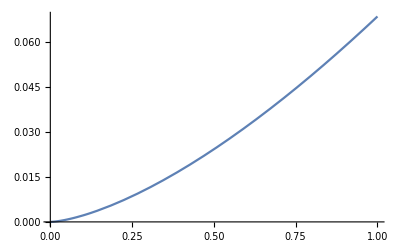

```mathematica
Plot[F[2,e,0.01],{e,-1,1},PlotRange->All]
```

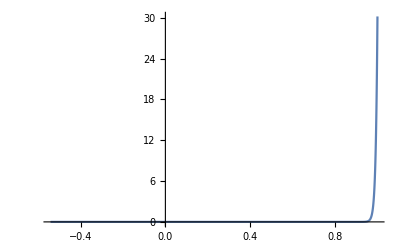

```mathematica
Plot[F[-121,e,0.01],{e,-1,1},PlotRange->All]
```

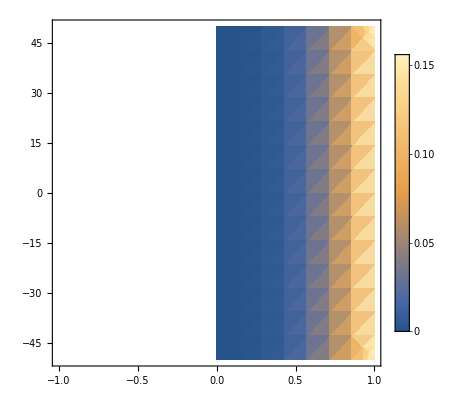

```mathematica
DensityPlot[F[0,e,l],{e,-1,1},{l,-50,50},PlotLegends->Automatic]
```

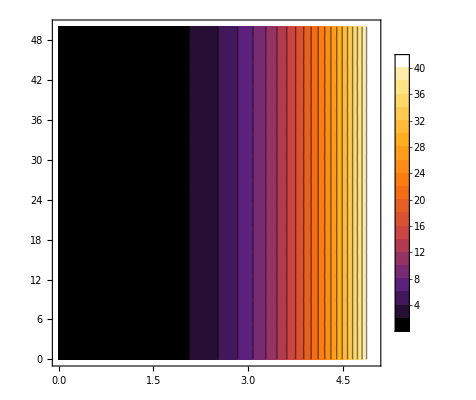

```mathematica
ContourPlot[F[0,e,l],{e,0,5},{l,0,50},PlotLegends->Automatic,Contours->20,ColorFunction->"Heat"]
```

```mathematica
(*
Corresponding Potential
Dejonghe,H.1987,MNRAS 224,13
*)
```

```mathematica
Psi[r_]:=1/Sqrt[1+r^2]
```

```mathematica
(*Mass density*)
```

```mathematica
Rho[r_]:=3/(4*Pi)*(1+r^2)^(-5/2)
```

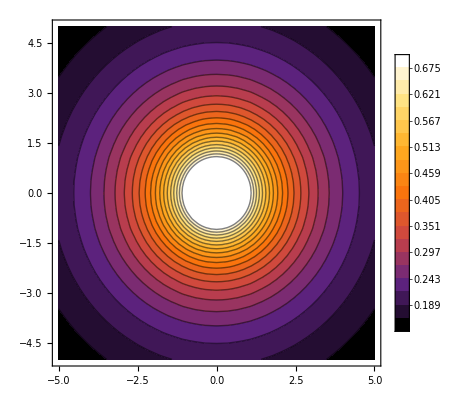

```mathematica
ContourPlot[Psi[Sqrt[x^2+y^2]],{x,-5,5},{y,-5,5},PlotLegends->Automatic,Contours->20,ColorFunction->"Heat"]
```

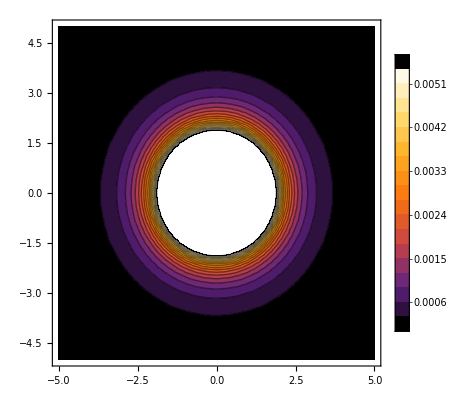

```mathematica
ContourPlot[Rho[Sqrt[x^2+y^2]],{x,-5,5},{y,-5,5},PlotLegends->Automatic,Contours->20,ColorFunction->"Heat"]
```

```mathematica
En[r_,vr_,vt_]:=Psi[r]-vr^2/2-vt^2/2
```

```mathematica
AngM[r_,vr_,vt_]:=r*vt
```

5

0

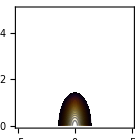

1

```mathematica
vm=5
ray=0
ContourPlot[En[ray,vr,vt],{vr,-vm,vm},{vt,0,vm},PlotLegends->Automatic,Contours->50,ColorFunction->"Heat",PlotRange->{{-vm,vm},{0,vm},{0,2}},ImageSize->140]
En[ray,0,0]
```

```mathematica
vmax1[vr_,vt_,r_]:=(vr+vt)-Sqrt[2*(vr*vt+Psi[r])]
vmax2[vr_,vt_,r_]:=(vr+vt)+Sqrt[2*(vr*vt+Psi[r])]
```

20

0

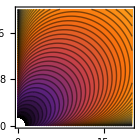

```mathematica
vm=20
ray=0
ContourPlot[vmax1[vr,vt,ray],{vr,0,vm},{vt,0,vm},PlotLegends->Automatic,Contours->50,ColorFunction->"Heat",PlotRange->{{0,vm},{0,vm},{0,20}},ImageSize->140]
```

20

0

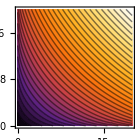

```mathematica
vm=20
ray=0
ContourPlot[vmax2[vr,vt,ray],{vr,0,vm},{vt,0,vm},PlotLegends->Automatic,Contours->50,ColorFunction->"Heat",PlotRange->{{0,vm},{0,vm},{0,100}},ImageSize->140]
```

```mathematica
dvmax[vr_,vt_,r_]:=Sqrt[2*(vr*vt+Psi[r])]
```

20

0

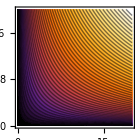

```mathematica
vm=20
ray=0
ContourPlot[dvmax[vr,vt,ray],{vr,0,vm},{vt,0,vm},PlotLegends->Automatic,Contours->50,ColorFunction->"Heat",PlotRange->{{0,vm},{0,vm},All},ImageSize->140]
```

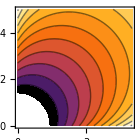

√2

```mathematica
vm=5;
ray=0;
ContourPlot[vmax1[vr,vt,ray],{vr,0,vm},{vt,0,vm},PlotLegends->Automatic,Contours->30,ColorFunction->"Heat",PlotRange->{{0,vm},{0,vm},{0,10}},ImageSize->140]
Sqrt[2*Psi[ray]]
```

```mathematica
vr[E_,L_,r_]:=Sqrt[2*(Psi[r]-E)-L^2/r^2]
vt[E_,L_,r_]:=L/r;
```

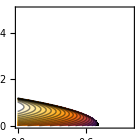

0.707107

1.18921

```mathematica
Lm=5;
ray=1;
ContourPlot[vmax2[vr[Eo,Lo,ray],vt[Eo,Lo,ray],ray],{Eo,0,1},{Lo,0,Lm},PlotLegends->Automatic,Contours->20,ColorFunction->"Heat",PlotRange->{{0,1},{0,Lm},All},ImageSize->140]
N[Psi[ray]]
N[Sqrt[2*(Psi[ray])]]
```

```mathematica
Lm=5;
ray=0.01;
ContourPlot[vmax1[vr[Eo,Lo,ray],vt[Eo,Lo,ray],ray],{Eo,0,1},{Lo,0,Lm},PlotLegends->Automatic,Contours->20,ColorFunction->"Heat",PlotRange->{{0,1},{0,Lm},{0,10}},ImageSize->140]
```

-Graphics-

1

1

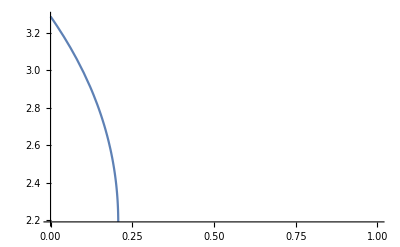

```mathematica
ray=1
Lo=1
Plot[vmax2[vr[Eo,Lo,ray],vt[Eo,Lo,ray],ray],{Eo,0,1},PlotRange->{{0,1},Automatic}]
```

```mathematica
Psieff[r_,L_]:=Psi[r]-L^2/(2*r^2)
```

```mathematica
Ecirc[L_]:=N[Maximize[Psieff[r,L],r]][[1]]
```

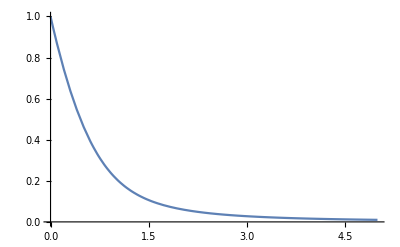

```mathematica
Lom=5;
Plot[Ecirc[Lo],{Lo,0,Lom},PlotRange->{All,{0,1}}]
```

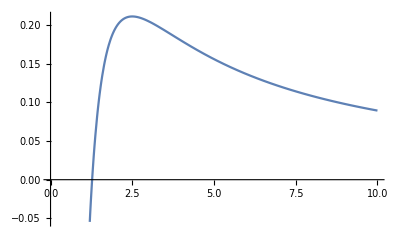

```mathematica
Plot[Psieff[r,1],{r,0,10}]
```

```mathematica
D[Psieff[r,L],r]
```

L^2/r^3-r/((1+r^2)^(3/2))

```mathematica
dP[r_,L_]:=L^2/r^3-r/((1+r^2)^(3/2))
```

```mathematica
D[D[Psieff[r,L],r],r]
```

-(3 L^2)/r^4+(3 r^2)/((1+r^2)^(5/2))-1/((1+r^2)^(3/2))

```mathematica
Manipulate[Plot[-(3 L^2)/r^4+(3 r^2)/((1+r^2)^(5/2))-1/((1+r^2)^(3/2)),{r,-1.9547696883562478,1.9546807598458704}],{L,-0.6044906946585611,0.6044906817394577}]
```

```mathematica
d2P[r_,L_]:=-(3 L^2)/r^4+(3 r^2)/((1+r^2)^(5/2))-1/((1+r^2)^(3/2))
```

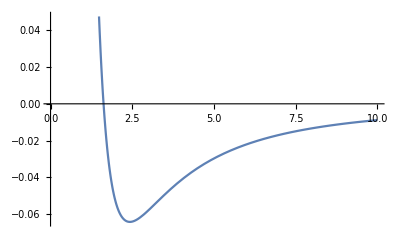

```mathematica
Plot[dP[r,1],{r,0,10},PlotRange->Automatic]
```